```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY207/sec_int_data/368nm.dat"]
```

{{1.65577,-1.0827},{1.59352,-1.04777},{1.51672,-0.974211},{1.46373,-0.892867},{1.42047,-0.88143},{1.37769,-0.829677},{1.34607,-0.781782},{1.31418,-0.77692},{1.27734,-0.771001},{1.24989,-0.775052},{1.21939,-0.707307},{1.20221,-0.744841},{1.18519,-0.864481},{1.17023,-0.902117},{1.1572,-0.972729},{1.14604,-1.02736},{1.13497,-1.12621},{1.12762,-1.64072},{1.12192,-1.5437},{1.11852,-1.34327},{1.11638,-1.28302},{1.11532,-1.27447},{1.11466,-0.870481},{1.11691,-0.769057},{1.12052,-0.628484},{1.12514,-0.556067},{1.15252,-0.613911},{1.18204,-0.657182},{1.20774,-0.608806},{1.24068,-0.598219},{1.28541,-0.636464},{1.36328,-0.692607},{1.4246,-0.732928}}

-1.17272+0.219805 x

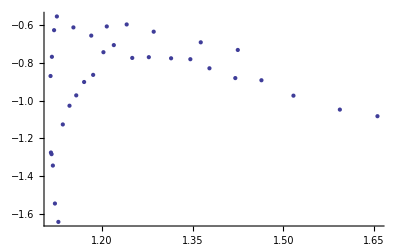

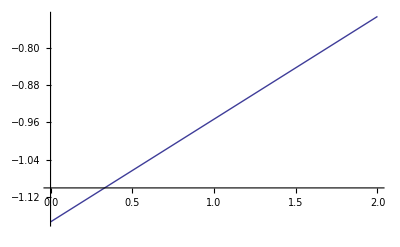

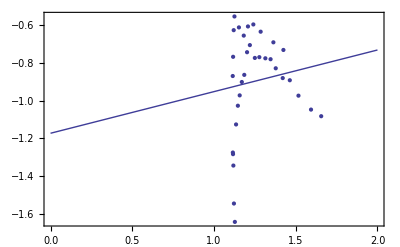

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```